```mathematica
(*Specify folder structure and filenames*)
Clear[ Filename, Filepath, rawData, partitionedData, partitionedData2, ArrayUnitsToMM, UnitsToMM];
Filename = "m4-steerer-5A";
Filepath = NotebookDirectory[]<>"../data/";
(*Import raw Data, still needs to be cleaned and re-ordered*)
rawData = Import[Filepath<> Filename <> ".txt", "Table"];

(*Ignore first 2 lines (metadata) and re-order it by x-value first and y-value scond*)
partitionedData =Partition[SortBy[Drop[rawData, 2], #[[2]]*100 + #[[1]]& ], 51];

(*partitionedData = Map[Function[x, Take[x, 4]], partitionedData];*)

ArrayUnitsToMM[a_, b_, c_] := UnitsToMM[#, b, c] &/@ a;
UnitsToMM[a_, b_, c_] := {(a[[1]]-1) * b, (a[[2]]-1) * c, Round[a[[3]] * (-1), 0.001]};

(*Scale x values from value# to mm*)
partitionedData =  Flatten[ArrayUnitsToMM[#, 10, 2] &/@ partitionedData,1];
ListContourPlot[partitionedData,InterpolationOrder->3, ColorFunction->"DarkRainbow", FrameLabel->{"x in mm","y in mm"},
AspectRatio -> 1/2.5, ContourLabels->All, Contours->{0.2,0.3,0.5, 1, 1.5, 2, 3, 4, 5.25, 6.5, 7, 7.2, 7.25, 7.3, 7.4,7.5, 7.6, 7.7, 7.8, 7.9, 8}]
```

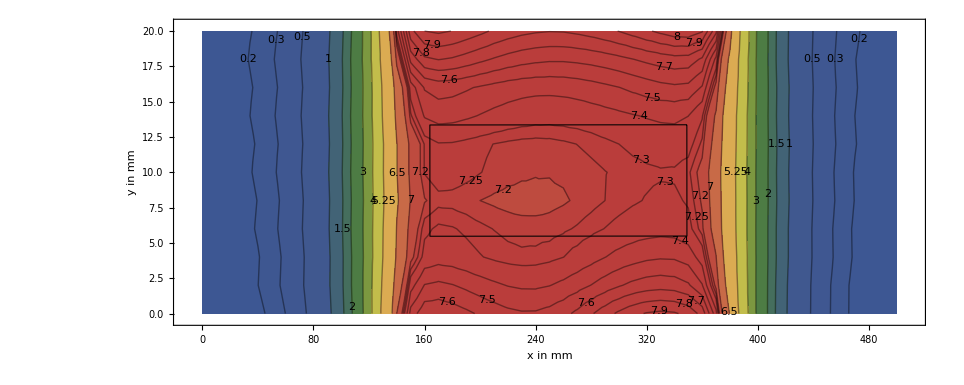

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[Function[y, ToString[y]]].

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

StringJoin::string: String expected at position 3 in 1 <> 1 <> (-0.0645) <> 2 <> 1 <> (-0.0827) <> 3 <> 1 <> (-0.1053) <> 4 <> 1 <> (-0.1344) <> 5 <> 1 <> (-0.1727) <> 6 <> 1 <> (-0.2258) <> 7 <> 1 <> (-0.3021) <> 8 <> 1 <> (-0.415) <> 9 <> 1 <> (-0.5886) <> 10 <> 1 <> (-0.8687) <> 11 <> 1 <> (-1.3415) <> 12 <> 1 <> (-2.1688) <> 13 <> 1 <> (-3.582) <> 14 <> 1 <> (-5.536) <> 15 <> 1 <> (-7.002) <> 16 <> 1 <> (-7.541) <> 17 <> 1 <> « 1633 ».

StringJoin::string: String expected at position 2 in 1 <> 1 <> (-0.0645) <> 2 <> 1 <> (-0.0827) <> 3 <> 1 <> (-0.1053) <> 4 <> 1 <> (-0.1344) <> 5 <> 1 <> (-0.1727) <> 6 <> 1 <> (-0.2258) <> 7 <> 1 <> (-0.3021) <> 8 <> 1 <> (-0.415) <> 9 <> 1 <> (-0.5886) <> 10 <> 1 <> (-0.8687) <> 11 <> 1 <> (-1.3415) <> 12 <> 1 <> (-2.1688) <> 13 <> 1 <> (-3.582) <> 14 <> 1 <> (-5.536) <> 15 <> 1 <> (-7.002) <> 16 <> 1 <> (-7.541) <> 17 <> 1 <> « 1633 ».

StringJoin::string: String expected at position 1 in 1 <> 1 <> (-0.0645) <> 2 <> 1 <> (-0.0827) <> 3 <> 1 <> (-0.1053) <> 4 <> 1 <> (-0.1344) <> 5 <> 1 <> (-0.1727) <> 6 <> 1 <> (-0.2258) <> 7 <> 1 <> (-0.3021) <> 8 <> 1 <> (-0.415) <> 9 <> 1 <> (-0.5886) <> 10 <> 1 <> (-0.8687) <> 11 <> 1 <> (-1.3415) <> 12 <> 1 <> (-2.1688) <> 13 <> 1 <> (-3.582) <> 14 <> 1 <> (-5.536) <> 15 <> 1 <> (-7.002) <> 16 <> 1 <> (-7.541) <> 17 <> 1 <> « 1633 ».

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

Drop::normal: Nonatomic expression expected at position 1 in Drop[2, $Failed].

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, 2].

Import::nffil: File not found during Import.

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

Drop::normal: Nonatomic expression expected at position 1 in Drop[2, $Failed].

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, 2].

Import::nffil: File not found during Import.

NotebookDirectory::nosv: The notebook xwp_shm is not saved.

StringJoin::string: String expected at position 1 in $Failed <> "../".

StringJoin::string: String expected at position 1 in $Failed <> "../m4-steerer-5A.txt".

Import::chtype: First argument $Failed <> "../m4-steerer-5A.txt" is not a valid file, directory, or URL specification.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, 2].

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[2, $Failed].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.